# Modeling Ski Slopes

## Topographic Map and Contour Plot

```mathematica
wasatch =GeoElevationData[{{41.133283,-111.875131},{40.983789,-111.767523}}]
```

StructuredArray[QuantityArray, {435, 313}, <Meters>]

```mathematica
elevations = Reverse@QuantityMagnitude[wasatch]
```

{1}
 |  |  |  |

```mathematica
elevationsflat = Flatten[elevations]
```

{1521.,1532.,1547.,1565.,1578.,1588.,1598.,1610.,1631.,1656.,1678.,1695.,1713.,1732.,1754.,1774.,1794.,1813.,1831.,1848.,1861.,136113,1494.,1496.,1498.,1499.,1499.,1497.,1496.,1496.,1496.,1497.,1496.,1496.,1497.,1499.,1506.,1515.,1521.,1524.,1524.,1524.,1527.}
 |  |  |  |

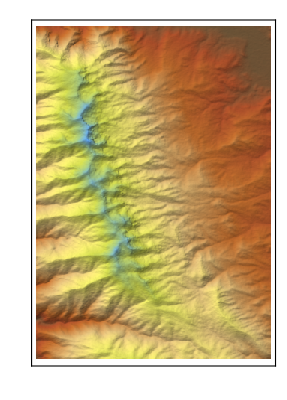

```mathematica
ReliefPlot[elevations, ColorFunction->"SouthwestColors"]
```

```mathematica
ListPlot3D[elevations, ColorFunction->"SouthwestColors"]
```

-Graphics3D-

```mathematica
ListPlot3D[elevations,MeshFunctions->{#3&},Mesh->40]
```

-Graphics3D-

## Turning the Slopes into a 3D Function

```mathematica
elevderiv = Transpose[{
Flatten[Table[Table[i,313],{i,435}]],
Flatten[Table[Table[q,{q,1,313,1}],435]],
GaussianFilter[elevationsflat,0.8]
}]
if = Interpolation[elevderiv]
dx=Derivative[0,0][if]
```

{{1,1,1521.76},{1,2,1532.28},{1,3,1547.21},{1,4,1564.66},{1,5,1577.79},136145,{435,309,1520.79},{435,310,1523.79},{435,311,1524.},{435,312,1524.21},{435,313,1526.79}}
 |  |  |  |

InterpolatingFunction[{{1., 435.}, {1., 313.}}, <>]

InterpolatingFunction[{{1., 435.}, {1., 313.}}, <>]

```mathematica
Plot3D[dx[x,y],{x,0,435},{y,0,313},ColorFunction->Function[{x,y,z},Hue[z]]]
```

InterpolatingFunction::dmval: Input value {0.0311025,0.0223795} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics3D-

## Slope Map: Shows where slopes are steep and where they are flat

```mathematica
dx=Derivative[1,0][if]
Plot3D[dx[x,y],{x,0,435},{y,0,313},ColorFunction->Function[{x,y,z},Hue[z]]]
```

InterpolatingFunction[{{1., 435.}, {1., 313.}}, <>]

InterpolatingFunction::dmval: Input value {0.0311025,0.0223795} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics3D-

## Locating Forestation

```mathematica
ColorReplace[ColorConvert[-Graphics-,"Grayscale"],Black->Pink]
```

-Graphics-